```mathematica
a[n_Integer]=FullSimplify[1/(n)(2ⅈ*k*a[n-1]+(n-2)a[n-2])];
a[0]=0;
a[1]=ⅈ*k;
```

```mathematica
Poly1=Expand[a[10]]
```

-(563 k^2)/1575+(1436 k^4)/2835-(86 k^6)/675+(8 k^8)/945-(2 k^10)/14175

```mathematica
Poly2=Expand[a[18]]
```

-(1593269 k^2)/6891885+(318710248 k^4)/638512875-(1322978884 k^6)/5746615875+(776008 k^8)/21049875-(33622 k^10)/13395375+(35272 k^12)/442047375-(332 k^14)/273648375+(16 k^16)/1915538625-(2 k^18)/97692469875

```mathematica
ImExact:=2 √(20*36)NIntegrate[Im[ⅇ^(ⅈ *x* k)1/(k Sinh[k*π])Poly1*Poly2],{k,0,100}];
ReExact:=2 √(20*36)NIntegrate[Re[ⅇ^(ⅈ *x* k)1/(k Sinh[k*π])Poly1*Poly2],{k,0,100}];.10.10
```

(.10)^2

```mathematica
a4=(255 √5 ⅇ^(5 ⅈ √2 x))/1024-51/64 √5 ⅇ^(6 ⅈ √2 x)+(3927 √5 ⅇ^(7 ⅈ √2 x))/4096-33/64 √5 ⅇ^(8 ⅈ √2 x)+(429 √5 ⅇ^(9 ⅈ √2 x))/4096;
```

```mathematica
a6=(357 √5 ⅇ^(4 ⅈ √2 x))/4096-(2397 √5 ⅇ^(5 ⅈ √2 x))/8192+(19125 √5 ⅇ^(6 ⅈ √2 x))/32768-(29421 √5 ⅇ^(7 ⅈ √2 x))/32768+(3597 √5 ⅇ^(8 ⅈ √2 x))/4096-(14751 √5 ⅇ^(9 ⅈ √2 x))/32768+(3003 √5 ⅇ^(10 ⅈ √2 x))/32768-(3825 ⅈ √(5/2) ⅇ^(5 ⅈ √2 x) x)/8192+459/256 ⅈ √(5/2) ⅇ^(6 ⅈ √2 x) x-(82467 ⅈ √(5/2) ⅇ^(7 ⅈ √2 x) x)/32768+99/64 ⅈ √(5/2) ⅇ^(8 ⅈ √2 x) x-(11583 ⅈ √(5/2) ⅇ^(9 ⅈ √2 x) x)/32768;
```

```mathematica
a8=(41769 √5 ⅇ^(3 ⅈ √2 x))/4194304+(1275 √5 ⅇ^(4 ⅈ √2 x))/32768-(3724887 √5 ⅇ^(5 ⅈ √2 x))/16777216+(261513 √5 ⅇ^(6 ⅈ √2 x))/524288-(10863363 √5 ⅇ^(7 ⅈ √2 x))/16777216+(13041 √5 ⅇ^(8 ⅈ √2 x))/32768+(30987 √5 ⅇ^(9 ⅈ √2 x))/16777216-(60489 √5 ⅇ^(10 ⅈ √2 x))/524288+(627627 √5 ⅇ^(11 ⅈ √2 x))/16777216-(1071 ⅈ √(5/2) ⅇ^(4 ⅈ √2 x) x)/8192+(199665 ⅈ √(5/2) ⅇ^(5 ⅈ √2 x) x)/524288-(87669 ⅈ √(5/2) ⅇ^(6 ⅈ √2 x) x)/131072+(3045987 ⅈ √(5/2) ⅇ^(7 ⅈ √2 x) x)/2097152-(4257 ⅈ √(5/2) ⅇ^(8 ⅈ √2 x) x)/2048+(2919807 ⅈ √(5/2) ⅇ^(9 ⅈ √2 x) x)/2097152-(45045 ⅈ √(5/2) ⅇ^(10 ⅈ √2 x) x)/131072-(57375 √5 ⅇ^(5 ⅈ √2 x) x^2)/262144+(4131 √5 ⅇ^(6 ⅈ √2 x) x^2)/4096-(1731807 √5 ⅇ^(7 ⅈ √2 x) x^2)/1048576+297/256 √5 ⅇ^(8 ⅈ √2 x) x^2-(312741 √5 ⅇ^(9 ⅈ √2 x) x^2)/1048576;
```

```mathematica
a10=(1989 √5 ⅇ^(2 ⅈ √2 x))/4194304+(480063 √5 ⅇ^(3 ⅈ √2 x))/33554432-(25347 √5 ⅇ^(4 ⅈ √2 x))/4194304-(11454537 √5 ⅇ^(5 ⅈ √2 x))/134217728+(233325 √5 ⅇ^(6 ⅈ √2 x))/1048576-(28933149 √5 ⅇ^(7 ⅈ √2 x))/134217728-(23391 √5 ⅇ^(8 ⅈ √2 x))/524288+(31686741 √5 ⅇ^(9 ⅈ √2 x))/134217728-(579249 √5 ⅇ^(10 ⅈ √2 x))/4194304+(882453 √5 ⅇ^(11 ⅈ √2 x))/134217728+(40755 √5 ⅇ^(12 ⅈ √2 x))/4194304-(375921 ⅈ √(5/2) ⅇ^(3 ⅈ √2 x) x)/33554432-(55233 ⅈ √(5/2) ⅇ^(4 ⅈ √2 x) x)/524288+(69422985 ⅈ √(5/2) ⅇ^(5 ⅈ √2 x) x)/134217728-(10274175 ⅈ √(5/2) ⅇ^(6 ⅈ √2 x) x)/8388608+(272211219 ⅈ √(5/2) ⅇ^(7 ⅈ √2 x) x)/134217728-(477621 ⅈ √(5/2) ⅇ^(8 ⅈ √2 x) x)/262144+(62670267 ⅈ √(5/2) ⅇ^(9 ⅈ √2 x) x)/134217728+(2593305 ⅈ √(5/2) ⅇ^(10 ⅈ √2 x) x)/8388608-(20711691 ⅈ √(5/2) ⅇ^(11 ⅈ √2 x) x)/134217728-(3213 √5 ⅇ^(4 ⅈ √2 x) x^2)/65536+(837675 √5 ⅇ^(5 ⅈ √2 x) x^2)/8388608-(28917 √5 ⅇ^(6 ⅈ √2 x) x^2)/2097152+(12067083 √5 ⅇ^(7 ⅈ √2 x) x^2)/33554432-(18711 √5 ⅇ^(8 ⅈ √2 x) x^2)/16384+(35820873 √5 ⅇ^(9 ⅈ √2 x) x^2)/33554432-(675675 √5 ⅇ^(10 ⅈ √2 x) x^2)/2097152+(286875 ⅈ √(5/2) ⅇ^(5 ⅈ √2 x) x^3)/2097152-(12393 ⅈ √(5/2) ⅇ^(6 ⅈ √2 x) x^3)/16384+(12122649 ⅈ √(5/2) ⅇ^(7 ⅈ √2 x) x^3)/8388608-297/256 ⅈ √(5/2) ⅇ^(8 ⅈ √2 x) x^3+(2814669 ⅈ √(5/2) ⅇ^(9 ⅈ √2 x) x^3)/8388608;
```

```mathematica
a12=(153153 √5 ⅇ^(ⅈ √2 x))/17179869184+(570843 √5 ⅇ^(2 ⅈ √2 x))/536870912+(485011989 √5 ⅇ^(3 ⅈ √2 x))/34359738368-(63355617 √5 ⅇ^(4 ⅈ √2 x))/2147483648+(400069167 √5 ⅇ^(5 ⅈ √2 x))/68719476736+(63688815 √5 ⅇ^(6 ⅈ √2 x))/2147483648+(3325382571 √5 ⅇ^(7 ⅈ √2 x))/68719476736-(64520247 √5 ⅇ^(8 ⅈ √2 x))/268435456+(17959942377 √5 ⅇ^(9 ⅈ √2 x))/68719476736-(160423131 √5 ⅇ^(10 ⅈ √2 x))/2147483648-(2020321875 √5 ⅇ^(11 ⅈ √2 x))/68719476736+(25162137 √5 ⅇ^(12 ⅈ √2 x))/2147483648+(63047985 √5 ⅇ^(13 ⅈ √2 x))/34359738368-(5967 ⅈ √(5/2) ⅇ^(2 ⅈ √2 x) x)/16777216-(43210719 ⅈ √(5/2) ⅇ^(3 ⅈ √2 x) x)/2147483648-(162945 ⅈ √(5/2) ⅇ^(4 ⅈ √2 x) x)/4194304+(3067555995 ⅈ √(5/2) ⅇ^(5 ⅈ √2 x) x)/8589934592-(30965085 ⅈ √(5/2) ⅇ^(6 ⅈ √2 x) x)/33554432+(2811018231 ⅈ √(5/2) ⅇ^(7 ⅈ √2 x) x)/2147483648-(10416807 ⅈ √(5/2) ⅇ^(8 ⅈ √2 x) x)/16777216-(35943345 ⅈ √(5/2) ⅇ^(9 ⅈ √2 x) x)/67108864+(40437045 ⅈ √(5/2) ⅇ^(10 ⅈ √2 x) x)/67108864-(709336485 ⅈ √(5/2) ⅇ^(11 ⅈ √2 x) x)/8589934592-(366795 ⅈ √(5/2) ⅇ^(12 ⅈ √2 x) x)/8388608-(3383289 √5 ⅇ^(3 ⅈ √2 x) x^2)/1073741824-(119799 √5 ⅇ^(4 ⅈ √2 x) x^2)/2097152+(1123184475 √5 ⅇ^(5 ⅈ √2 x) x^2)/4294967296-(41361273 √5 ⅇ^(6 ⅈ √2 x) x^2)/67108864+(1431500553 √5 ⅇ^(7 ⅈ √2 x) x^2)/1073741824-(1769661 √5 ⅇ^(8 ⅈ √2 x) x^2)/1048576+(202583997 √5 ⅇ^(9 ⅈ √2 x) x^2)/268435456+(11679525 √5 ⅇ^(10 ⅈ √2 x) x^2)/67108864-(683485803 √5 ⅇ^(11 ⅈ √2 x) x^2)/4294967296+(3213 ⅈ √(5/2) ⅇ^(4 ⅈ √2 x) x^3)/131072-(1778625 ⅈ √(5/2) ⅇ^(5 ⅈ √2 x) x^3)/134217728-(2193561 ⅈ √(5/2) ⅇ^(6 ⅈ √2 x) x^3)/8388608+(109881765 ⅈ √(5/2) ⅇ^(7 ⅈ √2 x) x^3)/536870912+(1485 ⅈ √(5/2) ⅇ^(8 ⅈ √2 x) x^3)/2048-(580038327 ⅈ √(5/2) ⅇ^(9 ⅈ √2 x) x^3)/536870912+(3378375 ⅈ √(5/2) ⅇ^(10 ⅈ √2 x) x^3)/8388608+(4303125 √5 ⅇ^(5 ⅈ √2 x) x^4)/134217728-(111537 √5 ⅇ^(6 ⅈ √2 x) x^4)/524288+(254575629 √5 ⅇ^(7 ⅈ √2 x) x^4)/536870912-(891 √5 ⅇ^(8 ⅈ √2 x) x^4)/2048+(75996063 √5 ⅇ^(9 ⅈ √2 x) x^4)/536870912;
```

```mathematica
a14=(3621969 √5 ⅇ^(ⅈ √2 x))/137438953472+(428889957 √5 ⅇ^(2 ⅈ √2 x))/274877906944+(3255282621 √5 ⅇ^(3 ⅈ √2 x))/274877906944-(1295331105 √5 ⅇ^(4 ⅈ √2 x))/34359738368+(28722634407 √5 ⅇ^(5 ⅈ √2 x))/549755813888-(4920508485 √5 ⅇ^(6 ⅈ √2 x))/68719476736+(91363937763 √5 ⅇ^(7 ⅈ √2 x))/549755813888-(2408027493 √5 ⅇ^(8 ⅈ √2 x))/8589934592+(109464714225 √5 ⅇ^(9 ⅈ √2 x))/549755813888-(559942503 √5 ⅇ^(10 ⅈ √2 x))/137438953472-(26220843627 √5 ⅇ^(11 ⅈ √2 x))/549755813888+(218073141 √5 ⅇ^(12 ⅈ √2 x))/34359738368+(1045536921 √5 ⅇ^(13 ⅈ √2 x))/274877906944+(74687613 √5 ⅇ^(14 ⅈ √2 x))/274877906944-(459459 ⅈ √(5/2) ⅇ^(ⅈ √2 x) x)/137438953472-(1987011 ⅈ √(5/2) ⅇ^(2 ⅈ √2 x) x)/2147483648-(6589631205 ⅈ √(5/2) ⅇ^(3 ⅈ √2 x) x)/274877906944+(73565001 ⅈ √(5/2) ⅇ^(4 ⅈ √2 x) x)/4294967296+(88225304355 ⅈ √(5/2) ⅇ^(5 ⅈ √2 x) x)/549755813888-(16301653623 ⅈ √(5/2) ⅇ^(6 ⅈ √2 x) x)/34359738368+(271475705529 ⅈ √(5/2) ⅇ^(7 ⅈ √2 x) x)/549755813888+(338566887 ⅈ √(5/2) ⅇ^(8 ⅈ √2 x) x)/1073741824-(546129525987 ⅈ √(5/2) ⅇ^(9 ⅈ √2 x) x)/549755813888+(17425488465 ⅈ √(5/2) ⅇ^(10 ⅈ √2 x) x)/34359738368+(43831700055 ⅈ √(5/2) ⅇ^(11 ⅈ √2 x) x)/549755813888-(293949513 ⅈ √(5/2) ⅇ^(12 ⅈ √2 x) x)/4294967296-(2458871415 ⅈ √(5/2) ⅇ^(13 ⅈ √2 x) x)/274877906944-(17901 √5 ⅇ^(2 ⅈ √2 x) x^2)/268435456-(233356059 √5 ⅇ^(3 ⅈ √2 x) x^2)/34359738368-(10433529 √5 ⅇ^(4 ⅈ √2 x) x^2)/268435456+(35814049425 √5 ⅇ^(5 ⅈ √2 x) x^2)/137438953472-(6035262453 √5 ⅇ^(6 ⅈ √2 x) x^2)/8589934592+(5591375055 √5 ⅇ^(7 ⅈ √2 x) x^2)/4294967296-(74832039 √5 ⅇ^(8 ⅈ √2 x) x^2)/67108864-(3784557573 √5 ⅇ^(9 ⅈ √2 x) x^2)/34359738368+(5176865925 √5 ⅇ^(10 ⅈ √2 x) x^2)/8589934592-(19564138737 √5 ⅇ^(11 ⅈ √2 x) x^2)/137438953472-(3301155 √5 ⅇ^(12 ⅈ √2 x) x^2)/67108864+(10149867 ⅈ √(5/2) ⅇ^(3 ⅈ √2 x) x^3)/8589934592+(313497 ⅈ √(5/2) ⅇ^(4 ⅈ √2 x) x^3)/8388608-(5418093375 ⅈ √(5/2) ⅇ^(5 ⅈ √2 x) x^3)/34359738368+(166485375 ⅈ √(5/2) ⅇ^(6 ⅈ √2 x) x^3)/536870912-(16868050227 ⅈ √(5/2) ⅇ^(7 ⅈ √2 x) x^3)/17179869184+(974673 ⅈ √(5/2) ⅇ^(8 ⅈ √2 x) x^3)/524288-(20813178177 ⅈ √(5/2) ⅇ^(9 ⅈ √2 x) x^3)/17179869184-(39092625 ⅈ √(5/2) ⅇ^(10 ⅈ √2 x) x^3)/536870912+(7518343833 ⅈ √(5/2) ⅇ^(11 ⅈ √2 x) x^3)/34359738368+(9639 √5 ⅇ^(4 ⅈ √2 x) x^4)/2097152+(18073125 √5 ⅇ^(5 ⅈ √2 x) x^4)/2147483648-(40264857 √5 ⅇ^(6 ⅈ √2 x) x^4)/268435456+(2040689133 √5 ⅇ^(7 ⅈ √2 x) x^4)/8589934592+(15147 √5 ⅇ^(8 ⅈ √2 x) x^4)/131072-(3478281345 √5 ⅇ^(9 ⅈ √2 x) x^4)/8589934592+(50675625 √5 ⅇ^(10 ⅈ √2 x) x^4)/268435456-(12909375 ⅈ √(5/2) ⅇ^(5 ⅈ √2 x) x^5)/1073741824-(21011507935 ⅈ √(5/2) ⅇ^(6 ⅈ √2 x) x^5)/2147483648+(106085464667 ⅈ ⅇ^(6 ⅈ √2 x) x^5)/(2147483648 √10)-(6172478235 ⅈ √(5/2) ⅇ^(7 ⅈ √2 x) x^5)/1073741824+(118103476491 ⅈ ⅇ^(7 ⅈ √2 x) x^5)/(4294967296 √10)-(183889930455 ⅈ √(5/2) ⅇ^(8 ⅈ √2 x) x^5)/2147483648+(922252495923 ⅈ ⅇ^(8 ⅈ √2 x) x^5)/(2147483648 √10)-(41992878785 ⅈ √(5/2) ⅇ^(9 ⅈ √2 x) x^5)/4294967296+(203039551 ⅈ ⅇ^(9 ⅈ √2 x) x^5)/(4194304 √10);
```

```mathematica
a16=(6861518937 √5 ⅇ^(ⅈ √2 x))/140737488355328+(8389611129 √5 ⅇ^(2 ⅈ √2 x))/4398046511104+(2527409816883 √5 ⅇ^(3 ⅈ √2 x))/281474976710656-(646104087 √5 ⅇ^(4 ⅈ √2 x))/17179869184+(19760863408767 √5 ⅇ^(5 ⅈ √2 x))/281474976710656-(62286344169 √5 ⅇ^(6 ⅈ √2 x))/549755813888+(27972702099237 √5 ⅇ^(7 ⅈ √2 x))/140737488355328-(17107872327 √5 ⅇ^(8 ⅈ √2 x))/68719476736+(16709033707155 √5 ⅇ^(9 ⅈ √2 x))/140737488355328+(102866444559 √5 ⅇ^(10 ⅈ √2 x))/2199023255552-(13867451835039 √5 ⅇ^(11 ⅈ √2 x))/281474976710656-(124177053 √5 ⅇ^(12 ⅈ √2 x))/68719476736+(1329093803037 √5 ⅇ^(13 ⅈ √2 x))/281474976710656+(3415260849 √5 ⅇ^(14 ⅈ √2 x))/4398046511104+(4662640983 √5 ⅇ^(15 ⅈ √2 x))/140737488355328-(97494813 ⅈ √(5/2) ⅇ^(ⅈ √2 x) x)/8796093022208-(1682353575 ⅈ √(5/2) ⅇ^(2 ⅈ √2 x) x)/1099511627776-(420795815697 ⅈ √(5/2) ⅇ^(3 ⅈ √2 x) x)/17592186044416+(14411203641 ⅈ √(5/2) ⅇ^(4 ⅈ √2 x) x)/274877906944+(9244275705 ⅈ √(5/2) ⅇ^(5 ⅈ √2 x) x)/1099511627776-(62087338701 ⅈ √(5/2) ⅇ^(6 ⅈ √2 x) x)/549755813888-(772546547871 ⅈ √(5/2) ⅇ^(7 ⅈ √2 x) x)/8796093022208+(13949429193 ⅈ √(5/2) ⅇ^(8 ⅈ √2 x) x)/17179869184-(4504093381935 ⅈ √(5/2) ⅇ^(9 ⅈ √2 x) x)/4398046511104+(68006512935 ⅈ √(5/2) ⅇ^(10 ⅈ √2 x) x)/274877906944+(3660530841 ⅈ √(5/2) ⅇ^(11 ⅈ √2 x) x)/17179869184-(15535795275 ⅈ √(5/2) ⅇ^(12 ⅈ √2 x) x)/274877906944-(382761561897 ⅈ √(5/2) ⅇ^(13 ⅈ √2 x) x)/17592186044416-(1568439873 ⅈ √(5/2) ⅇ^(14 ⅈ √2 x) x)/1099511627776-(1378377 √5 ⅇ^(ⅈ √2 x) x^2)/4398046511104-(6784479 √5 ⅇ^(2 ⅈ √2 x) x^2)/34359738368-(82906910343 √5 ⅇ^(3 ⅈ √2 x) x^2)/8796093022208-(475417971 √5 ⅇ^(4 ⅈ √2 x) x^2)/34359738368+(412264609875 √5 ⅇ^(5 ⅈ √2 x) x^2)/2199023255552-(149132262159 √5 ⅇ^(6 ⅈ √2 x) x^2)/274877906944+(7633406671821 √5 ⅇ^(7 ⅈ √2 x) x^2)/8796093022208-(20788461 √5 ⅇ^(8 ⅈ √2 x) x^2)/67108864-(6911243529471 √5 ⅇ^(9 ⅈ √2 x) x^2)/8796093022208+(190475121375 √5 ⅇ^(10 ⅈ √2 x) x^2)/274877906944+(5174963937 √5 ⅇ^(11 ⅈ √2 x) x^2)/274877906944-(3252958137 √5 ⅇ^(12 ⅈ √2 x) x^2)/34359738368-(95895985185 √5 ⅇ^(13 ⅈ √2 x) x^2)/8796093022208+(17901 ⅈ √(5/2) ⅇ^(2 ⅈ √2 x) x^3)/1073741824+(1633583295 ⅈ √(5/2) ⅇ^(3 ⅈ √2 x) x^3)/549755813888+(18656055 ⅈ √(5/2) ⅇ^(4 ⅈ √2 x) x^3)/536870912-(473350584375 ⅈ √(5/2) ⅇ^(5 ⅈ √2 x) x^3)/2199023255552+(20237667669 ⅈ √(5/2) ⅇ^(6 ⅈ √2 x) x^3)/34359738368-(3123208691757 ⅈ √(5/2) ⅇ^(7 ⅈ √2 x) x^3)/2199023255552+(120394647 ⅈ √(5/2) ⅇ^(8 ⅈ √2 x) x^3)/67108864-(839061233541 ⅈ √(5/2) ⅇ^(9 ⅈ √2 x) x^3)/2199023255552-(25719271875 ⅈ √(5/2) ⅇ^(10 ⅈ √2 x) x^3)/34359738368+(603332960373 ⅈ √(5/2) ⅇ^(11 ⅈ √2 x) x^3)/2199023255552+(9903465 ⅈ √(5/2) ⅇ^(12 ⅈ √2 x) x^3)/134217728+(91348803 √5 ⅇ^(3 ⅈ √2 x) x^4)/549755813888+(290547 √5 ⅇ^(4 ⅈ √2 x) x^4)/33554432-(69198553125 √5 ⅇ^(5 ⅈ √2 x) x^4)/2199023255552+(9100107 √5 ⅇ^(6 ⅈ √2 x) x^4)/536870912-(440523386163 √5 ⅇ^(7 ⅈ √2 x) x^4)/2199023255552+(2957877 √5 ⅇ^(8 ⅈ √2 x) x^4)/4194304-(1419974745453 √5 ⅇ^(9 ⅈ √2 x) x^4)/2199023255552+(36196875 √5 ⅇ^(10 ⅈ √2 x) x^4)/1073741824+(248105346489 √5 ⅇ^(11 ⅈ √2 x) x^4)/2199023255552-(286712055 ⅈ √(5/2) ⅇ^(4 ⅈ √2 x) x^5)/137438953472+(486008019 ⅈ ⅇ^(4 ⅈ √2 x) x^5)/(137438953472 √10)-(513793125 ⅈ √(5/2) ⅇ^(5 ⅈ √2 x) x^5)/68719476736+(109417797 ⅈ √(5/2) ⅇ^(6 ⅈ √2 x) x^5)/1073741824-(27448360292871 ⅈ √(5/2) ⅇ^(7 ⅈ √2 x) x^5)/1099511627776+(136064289800439 ⅈ ⅇ^(7 ⅈ √2 x) x^5)/(1099511627776 √10)+(4278948672339 ⅈ √(5/2) ⅇ^(8 ⅈ √2 x) x^5)/17179869184-(21392641228959 ⅈ ⅇ^(8 ⅈ √2 x) x^5)/(17179869184 √10)-(5206492789751 ⅈ √(5/2) ⅇ^(9 ⅈ √2 x) x^5)/5772436045824+(32158341193 ⅈ ⅇ^(9 ⅈ √2 x) x^5)/(5637144576 √10)-(152026875 ⅈ √(5/2) ⅇ^(10 ⅈ √2 x) x^5)/1073741824-(64546875 √5 ⅇ^(5 ⅈ √2 x) x^6)/34359738368+(9653777284697 ⅇ^(6 ⅈ √2 x) x^6)/(412316860416 √5)-(1923354396997 √5 ⅇ^(6 ⅈ √2 x) x^6)/412316860416-(1535345194383 ⅇ^(7 ⅈ √2 x) x^6)/(137438953472 √5)+(37448064423 √5 ⅇ^(7 ⅈ √2 x) x^6)/17179869184+(47034877292073 ⅇ^(8 ⅈ √2 x) x^6)/(137438953472 √5)-(9398006358741 √5 ⅇ^(8 ⅈ √2 x) x^6)/137438953472-(3451672367 ⅇ^(9 ⅈ √2 x) x^6)/(100663296 √5)+(2816529777061 √5 ⅇ^(9 ⅈ √2 x) x^6)/412316860416;
```

```mathematica
Exa=Plot[ReExact,{x,0,2}];
```

```mathematica
Disc=Plot[Re[a4+a6+a8+a10+a12+a14+a16],{x,0,2},PlotStyle->{Red}];
```

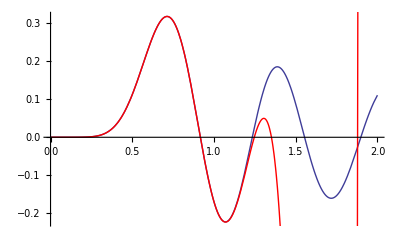

```mathematica
Show[Exa,Disc]
```

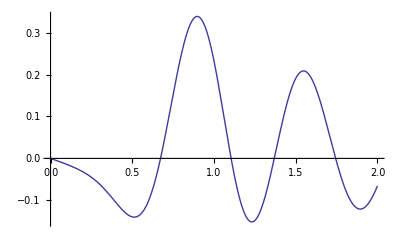

```mathematica
ExIm=Plot[ImExact,{x,0,2}]
```

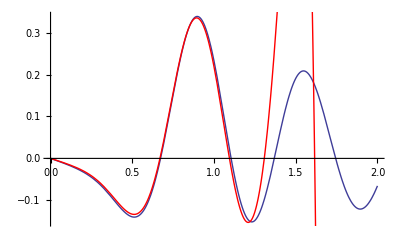

```mathematica
DiscIm=Plot[Im[a4+a6+a8+a10+a12+a14+a16-ⅈ*x*0.04-ⅈ*x^3*0.04-ⅈ*x^5*0.04-ⅈ*x^7*0.04],{x,0,2},PlotStyle->{Red}];
Show[ExIm,DiscIm]
```